```mathematica
SetDirectory[NotebookDirectory[]];
Import["init.wl"];
```

### Harmonic Oscillator

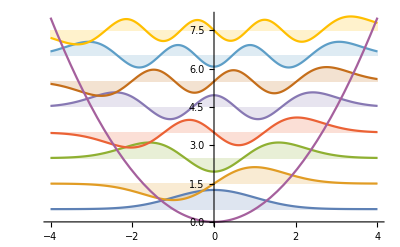

```mathematica
f[n_,x_]:=((1/Pi)^(1/4)HermiteH[n,x])/(E^(x^2/2)Sqrt[2^n n!])
Plot[Evaluate@
  Append[Table[f[n,x]+n+1/2,{n,0,7}],x^2/2],{x,-4,4},Filling->Table[n->n-1/2,{n,1,8}]]
```

### Particle in finite well

```mathematica
subs = {ρ -> √(-2 m en)/ℏ,k-> √(2m (en + Vo))};
ϕ1[x_]:= l1 Exp[ρ x] ;
ϕ2s[x_]:= w1 Cos[k x];
ϕ2a[x_]:= w1 Sin[k x];
ϕ3[x_]:=  r2 Exp[-ρ x];
```

```mathematica
sym =  {ϕ1[-a] - ϕ2s[-a] == 0,(D[ϕ1[x],x]-D[ϕ2s[x],x]==0)/.x-> -a}
```

{ⅇ^(-a ρ) l1-w1 Cos[a k]==0,ⅇ^(-a ρ) l1 ρ-k w1 Sin[a k]==0}

```mathematica
asym = {ϕ1[-a] - ϕ2a[-a] == 0,(D[ϕ1[x],x]-D[ϕ2a[x],x]==0)/.x-> -a}
```

{ⅇ^(-a ρ) l1+w1 Sin[a k]==0,ⅇ^(-a ρ) l1 ρ-k w1 Cos[a k]==0}

-9.7507 | S
-7.77297 | S
-3.94146 | S
-9.00542 | A
-6.07186 | A
-1.49125 | A

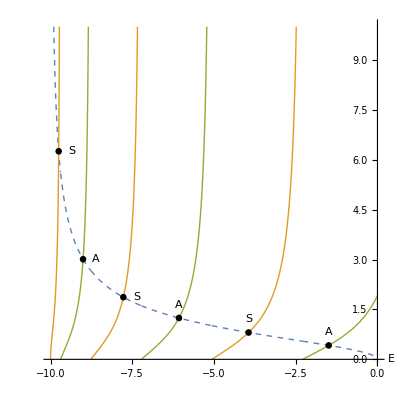

```mathematica
subs = {ρ -> √(-2 m en)/ℏ,k-> √(2m (en + Vo))};

f1[en_]:= √(-en/(en + Vo)) ;
fs[en_]:= Tan[a   √(2m (en + Vo))/ℏ ]/.subs;
fa[en_]:= -Cot[a  √(2m (en + Vo))/ℏ]/.subs;
params = {a-> 2,m-> 1, ℏ-> 1, Vo-> 10};

rs0 =  FindRoot[(f1[en]-fs[en]==0)/.params,{en,-9.999}]//Chop;
rs1 =  FindRoot[(f1[en]-fs[en]==0)/.params,{en,-8}]//Chop;
rs2 =  FindRoot[(f1[en]-fs[en]==0)/.params,{en,-4}]//Chop;

ra1 =  FindRoot[(f1[en]-fa[en]==0)/.params,{en,-9}]//Chop;
ra2 =  FindRoot[(f1[en]-fa[en]==0)/.params,{en,-6}]//Chop;
ra3 =  FindRoot[(f1[en]-fa[en]==0)/.params,{en,-2}]//Chop;


tab1 = {{en/.rs0,S},{en/.rs1,S},{en/.rs2,S},{en/.ra1,A},{en/.ra2,A},{en/.ra3,A}};
tab1//TableForm

p1 = {en/.rs0,f1[en/.rs0]/.params};
p2 = {en/.rs1,f1[en/.rs1]/.params};
p3 = {en/.rs2,f1[en/.rs2]/.params};
p4 = {en/.ra1,f1[en/.ra1]/.params};
p5 = {en/.ra2,f1[en/.ra2]/.params};
p6 = {en/.ra3,f1[en/.ra3]/.params};

Plot[{f1[x]/.params,
fs[x]/.params,
fa[x]/.params
},{x,-10,0},
PlotRange-> {0,10},
PlotStyle-> {{Thick,Dashing[{0.01}]},Thick,Thick},
AxesLabel-> {"E",None},
LabelStyle-> 16,
AspectRatio-> 1,
Exclusions-> {Sin[2 √(2(x+10))]==0,Cos[2 √(2(x+10))]==0},
PlotPoints->75,
Epilog-> {
Disk[{en/.rs0,f1[en/.rs0]/.params},0.1],
Disk[{en/.rs1,f1[en/.rs1]/.params},0.1],
Disk[{en/.rs2,f1[en/.rs2]/.params},0.1],
Disk[{en/.ra1,f1[en/.ra1]/.params},0.1],
Disk[{en/.ra2,f1[en/.ra2]/.params},0.1],
Disk[{en/.ra3,f1[en/.ra3]/.params},0.1],
Style[Text["S",p1+{0.4,0}],18],
Style[Text["S",p2+{0.4,0}],18],
Style[Text["S",p3+{0,0.4}],18],
Style[Text["A",p4+{0.4,0}],18],
Style[Text["A",p5+{0,0.4}],18],
Style[Text["A",p6+{0,0.4}],18],
AxesStyle-> Thick
}]
```

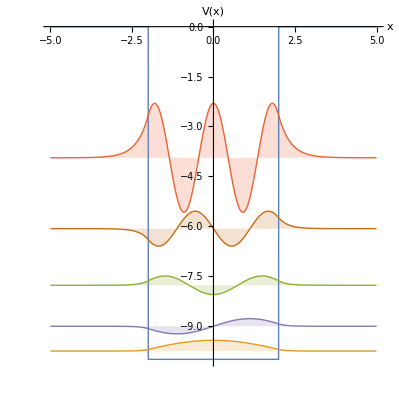

```mathematica
subs = {ρ-> √(-2 m en)/ℏ,k-> √(2m (en + Vo))}/.params;
ψs[x_]:= Which[
	Abs[x]< a, B Cos[  √(2m (en + Vo))x],
          x ≥ a,  Exp[-x √(-2 m en) ],
          x ≤ -a, Exp[ x √(-2 m en)]]/.{B-> Sec[a  √(2m (en + Vo))]Exp[-a √(-2 m en) ]}
ψa[x_]:= Which[
	Abs[x]≤  a, B Sin[ √(2 m (en+Vo)) x]/.subs,
          x > a,  Exp[-x √(-2 m en)],
          x < -a,-Exp[ x √(-2 m en)]]/.{B-> Csc[a √(2 m (en+Vo))/ℏ]Exp[-a √(-2 m en)/ℏ ]}
V[x_]:= If[Abs[x]< a, -Vo,0];

amp=350;
plotWF = Plot[{
V[x]/.params,
(amp ψs[x]+en)/.Join[params,rs0],
(amp  ψs[x]+en)/.Join[params,rs1],
(amp  ψs[x]+en)/.Join[params,rs2],
( amp ψa[x]+en)/.Join[params,ra1],
( amp ψa[x]+en)/.Join[params,ra2]
},{x,-5,5},
Filling->{
2->en/.Join[params,rs0],
3->en/.Join[params,rs1],
4->en/.Join[params,rs2],
5->en/.Join[params,ra1],
6->en/.Join[params,ra2],
},
PlotRange-> {1,-11},
LabelStyle-> 16,
AspectRatio-> {1},
PlotStyle-> Thick,
AxesLabel-> {"x","V(x)"}];
Show[plotWF]
```

### DOS versus dimensionality

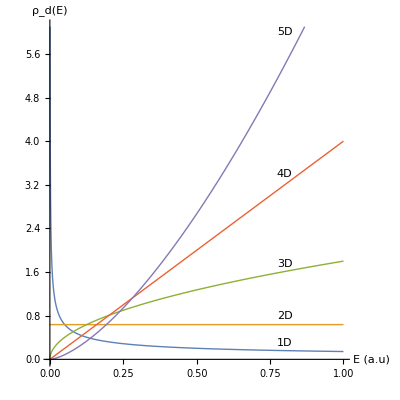

```mathematica
ρ[d_,x_]:= 2^(d/2-1)d π^(d/2-2)(√(m x)/ℏ)^d/(x Gamma[(d/2 +1)])
Plot[
{ρ[1,x]/.{m-> 1,ℏ-> 1},
ρ[2,x]/.{m-> 1,ℏ-> 1},
ρ[3,x]/.{m-> 1,ℏ-> 1},
ρ[4,x]/.{m-> 1,ℏ-> 1},
ρ[5,x]/.{m-> 1,ℏ-> 1}
},{x,0,1},
PlotStyle-> Thick,
AspectRatio-> 1,
AxesLabel-> {"E (a.u)","ρ_d(E)"},
LabelStyle-> 16,
Epilog-> {
Style[Text["1D",{0.8,0.3}],16],
Style[Text["2D",{0.8,0.8}],16],
Style[Text["3D",{0.8,1.75}],16],
Style[Text["4D",{0.8,3.4}],16],
Style[Text["5D",{0.8,6.0}],16]
}]
```